```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
data=Import["oscillator_waveform.csv","Dataset",HeaderLines->1];
```

```mathematica
t=Subdivide[-3.22*^-8,1.694*^-7,1007];
single=Normal[data[All,"single"]];
double=Normal[data[All,"double"]];
```

```mathematica
fontsize=36;
```

Plot single beam:

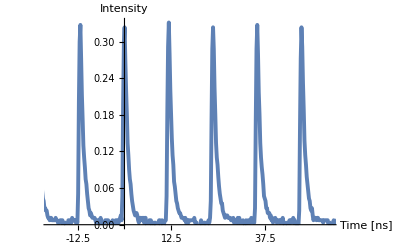

```mathematica
plot1=ListLinePlot[
Thread[{t,single}],Ticks->{Table[{12.5*10^-9*j,ToExpression[12.5*j],0.03,Directive[Black,Thick]},{j,-1,5}], None},
TicksStyle->Directive[fontsize,Black],
AxesLabel->{Style["Time\n[ns]",fontsize,Black],Style["Intensity",fontsize,Black]},
AxesStyle->{{Thick,Black},{Thick,Black}},
PlotRange->{{-20*^-9,55*^-9},{0,Max[single]}},
PlotStyle->Thickness[0.007],
ImageSize->{600},
AspectRatio->1/1.6
]
```

```mathematica
Export["single.pdf",plot1]
```

single.pdf

Same for double beam:

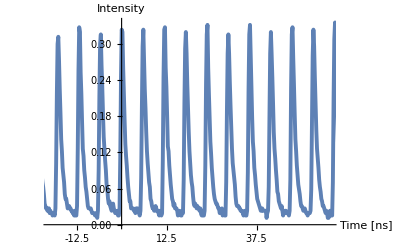

```mathematica
plot1=ListLinePlot[
Thread[{t,double}],Ticks->{Table[{12.5*10^-9*j,ToExpression[12.5*j],0.03,Directive[Black,Thick]},{j,-1,5}], None},
TicksStyle->Directive[fontsize,Black],
AxesLabel->{Style["Time\n[ns]",fontsize,Black],Style["Intensity",fontsize,Black]},
AxesStyle->{{Thick,Black},{Thick,Black}},
PlotRange->{{-20*^-9,58*^-9},{0,Max[double]}},
PlotStyle->Thickness[0.007],
ImageSize->{600},
AspectRatio->1/1.6
]
```